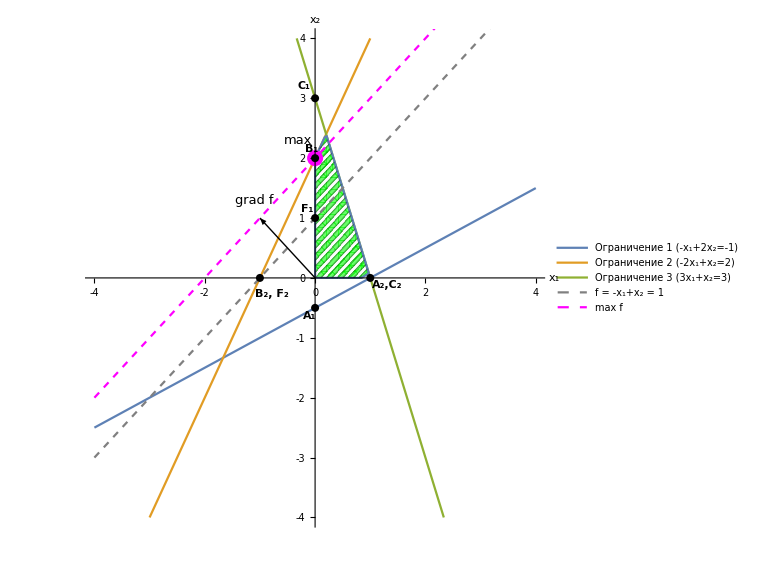

```mathematica
plot=Show[Plot[{-1/2+x/2,2+2x,3-3x},{x,-4,4},PlotRange->{{-4,4},{-4,4}},AspectRatio->Automatic,AxesLabel->{Style["x_1",Italic,14,Black],Style["x_2",Italic,14,Black]},PlotLegends->{"Ограничение 1 (-x_1+2x_2=-1)","Ограничение 2 (-2x_1+x_2=2)","Ограничение 3 (3x_1+x_2=3)"},Ticks->{Table[i,{i,-4,4}],Table[i,{i,-4,4}]}],
RegionPlot[-x+2y>=-1&&-2x+y<=2&&3x+y <=3&&x>=0&&y>=0,{x,-4,4},{y,-4,4},PlotRange->{{-4,4},{-4,4}},Mesh->30,MeshFunctions->{#1-#2&},MeshShading->{Directive[Green,Opacity[0.6]],None}],
Plot[{1+x,2+x},{x,-4,4},PlotStyle->{{Dashed,Gray},{Dashed,Magenta}},PlotLegends->{"f = -x_1+x_2 = 1","max f"}],
Graphics[{Arrow[{{0,0},{-1,1}}],Text[Style["grad f",Italic,13],{-1.1,1.3}]}],
Graphics[{Magenta,PointSize[0.02],Point[{0,2}],Black,Text[Style["max",Italic,13],{-0.3,2.3}]}],
Graphics[{PointSize[0.01],Point[{0,-1/2}],Text[Style["A_1",11,Bold],{-0.1,-0.64}]}],
Graphics[{PointSize[0.01],Point[{1,0}],Text[Style["A_2,C_2",11,Bold],{1.3,-0.11}]}],
Graphics[{PointSize[0.01],Point[{0,2}],Text[Style["B_1",11,Bold],{-0.07,2.15}]}],
Graphics[{PointSize[0.01],Point[{0,3}],Text[Style["C_1",11,Bold],{-0.2,3.2}]}],
Graphics[{PointSize[0.01],Point[{-1,0}],Text[Style["B_2, F_2",11,Bold],{-0.79,-0.27}]}],
Graphics[{PointSize[0.01],Point[{0,1}],Text[Style["F_1",11,Bold],{-0.15,1.15}]}],
ImageSize->Large]
```

```mathematica
Export["~/Downloads/plot.jpg",plot]
```

~/Downloads/plot.jpg